# What Is Quantum Computation?

Welcome to the first lesson of this course! We’ll start by briefly revisiting classical computation through clear, hands-on examples. Then, we’ll shift our focus to the quantum realm, where you’ll explore a few foundational quantum circuits. Each example will come with accompanying code; don’t worry if it doesn’t all make sense right away. As we progress, you’ll gradually build both your understanding of quantum concepts and your coding skills.

## Key Concepts

Quantum Circuit

Qubit

Measurement

## Classical Computation

In order to understand quantum computation, it helps to compare it to classical computation. To compute something, you have to be able to use rules to determine what should be the output from a list of inputs. You can think of computing as starting with the inputs and following the rules to reach an output.

Below is the definition of a simple function that accepts two binary strings as input and returns their sum also as a binary string:

Add two binary strings 01 and 01:

```mathematica
binAdd["01","01"]
```

10

Add two binary strings 100 and 011:

```mathematica
binAdd["100","011"]
```

111

This function is explicitly defined in terms of other Wolfram Language™ functions (see the end of this notebook). However, it is implicitly defined as a bunch of rules that tell you how to go from two binary strings of given lengths to some other binary string of a needed length:

binAdd:{0,1}^a×{0,1}^b↦{0,1}^c

## Classical Bits and Encodings

You may already be familiar with the fact that classical computations can be represented by operations on sequences of bits. A classical bit has a state which is either a 0 or a 1.

What are all the states of a sequence of four classical bits?

```mathematica
fourbits=StringJoin/@Tuples[{"0","1"},3]
```

{000,001,010,011,100,101,110,111}

It is also possible to encode information in such sequences of classical bits to represent problems of interest. For example, each of those bit sequences can encode an integer in the base-2 number system.

```mathematica
FromDigits[#,2]&/@fourbits
```

{0,1,2,3,4,5,6,7}

Each of those bit sequences could also encode letter characters with a different encoding scheme:

```mathematica
FromLetterNumber[FromDigits[#,2]]&/@fourbits
```

{ ,a,b,c,d,e,f,g}

With yet another encoding scheme, those same bit sequences could represent colors with opacity:

```mathematica
Apply[RGBColor,FromDigits/@Characters[#]]&/@fourbits
```

{RGBColor[0, 0, 0],RGBColor[0, 0, 1],RGBColor[0, 1, 0],RGBColor[0, 1, 1],RGBColor[1, 0, 0],RGBColor[1, 0, 1],RGBColor[1, 1, 0],RGBColor[1, 1, 1]}

As you can see, a lot of classical computing can be thought of as representing a problem of interest as a sequence of bits, using some rules to compute another sequence of bits, then decoding the result to get your solution. Let’s see one more example before moving on to quantum computation.

The usual Plus function doesn’t have rules for adding colors:

```mathematica
Red+Blue
```

RGBColor[0, 0, 1]+RGBColor[1, 0, 0]

Let’s define a function that encodes the colors as sequences of zeros and ones, performs a computation on those sequences, then decodes the result as another color. For illustration purposes this function uses Echo to show the intermediate bit sequences:

```mathematica
fblender[col1_,col2_]:=RGBColor@@Echo@MapThread[BitOr,Echo@MapApply[List,{col1,col2}]]
```

```mathematica
fblender[Red,Blue]
```

{{1,0,0},{0,0,1}}

{1,0,1}

RGBColor[1, 0, 1]

The code takes two RGBColor objects, extracts their red/green/blue numbers, does a bitwise OR on each pair of corresponding channels, and then builds a new RGBColor from the results.

## Quantum Circuits and Qubits

The diagram below represents an example of a  quantum circuit:

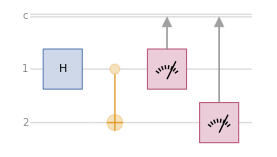

```mathematica
QuantumCircuitOperator[{"H","CNOT"->{1,2},{1},{2}}]["Diagram"]
```

Notice how the circuit diagram has several wires, labeled c, 1 and 2. Wires 1 and 2 represent qubits (quantum bits) instead of classical bits. The boxes that look like gauges on the right hand side of the diagram represent measurement and point to the wire labeled c. The wire labeled c represents a classical system (such as part of a regular computer) where the results of the measurements on qubits are stored. A quantum circuit is read from left to right. For example, the first operation—represented by the blue box labeled H, acts only on the first wire. All operations shown as boxes (except for measurements) are unitary and reversible, a key feature we’ll explore in more detail later. You can think of each box as performing a transformation on the quantum state of one or more wires. These transformations must obey fundamental principles dictated by quantum theory.

To create a circuit diagram like the one seen above, you first specify a circuit and then use the "Diagram" property of that circuit.

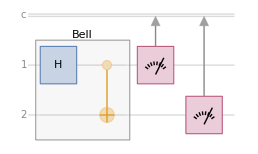

```mathematica
examplecircuit=QuantumCircuitOperator[{"Bell",{1},{2}}];
examplecircuit["Diagram"]
```

What are the results of running this circuit?

```mathematica
measurements=examplecircuit[]
```

QuantumMeasurement[…]

What you just saw was a quantum computation, carried out, of course, on a classical computer (your PC). This is exactly what a quantum simulator does: it mimics quantum behavior and performs computations using the rules of quantum mechanics, all within classical hardware.

Since the last operation in the circuit is a measurement, the result of evaluating the circuit is a QuantumMeasurement object. What are the results of the measurement in this circuit?

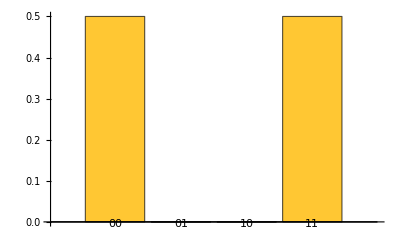

```mathematica
measurements["ProbabilitiesPlot"]
```

Notice that the possible outcomes of a quantum measurement are simply classical bit sequences. In the earlier classical computation examples, the rules were deterministic: each input led to a definite output. In contrast, quantum computation typically yields a range of possible outcomes, each with a certain probability. That’s because quantum theory, which underpins quantum computing, offers only a probabilistic description of measurement results.

For a quantum program to be useful, you want to arrange things so that the probability of measuring a result that encodes the solution to your problem is high.

```mathematica
measurements["Probabilities"]
```

<|00→1/2,01→0,10→0,11→1/2|>

In this example, the probability of obtaining “00” is 1/2, the probability of obtaining “11” is 1/2, and the probability of obtaining the “01” or “10” measurement outcomes is zero. While qubits are not the same as classical bits (otherwise quantum algorithms would be no different from classical ones), you will always perform some kind of measurement as part of a practical quantum circuit.

The other symbols in the quantum circuit represent instructions for what operations to perform on the qubits. The next lessons will discuss them in much greater detail.

### Example #1

Consider the quantum circuit below. What are the probabilities of measuring each of the 6-bit classical outcomes?

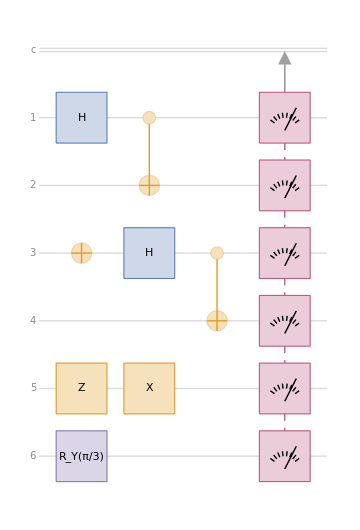

```mathematica
explorecircuit=QuantumCircuitOperator[{"H"->1,"NOT"->3,"CNOT"->{1,2},"H"->3,"CNOT"->{3,4},"Z"->5,"X"->5,"RY"[π/3]->6,"M"->Range[6]}];
explorecircuit["Diagram"]
```

##### Solution

To obtain all the possible measurement outcomes and their probabilities, evaluate the circuit and use the "Probabilities" property:

```mathematica
explorecircuit[]["Probabilities"]
```

<|000000→0,000001→0,000010→3/16,000011→1/16,000100→0,000101→0,000110→0,000111→0,001000→0,001001→0,001010→0,001011→0,001100→0,001101→0,001110→3/16,001111→1/16,010000→0,010001→0,010010→0,010011→0,010100→0,010101→0,010110→0,010111→0,011000→0,011001→0,011010→0,011011→0,011100→0,011101→0,011110→0,011111→0,100000→0,100001→0,100010→0,100011→0,100100→0,100101→0,100110→0,100111→0,101000→0,101001→0,101010→0,101011→0,101100→0,101101→0,101110→0,101111→0,110000→0,110001→0,110010→3/16,110011→1/16,110100→0,110101→0,110110→0,110111→0,111000→0,111001→0,111010→0,111011→0,111100→0,111101→0,111110→3/16,111111→1/16|>

To obtain only the nonzero probability outcomes, evaluate the circuit and use the "Probability" property:

```mathematica
explorecircuit[]["Probability"]
```

<|000010→3/16,000011→1/16,001110→3/16,001111→1/16,110010→3/16,110011→1/16,111110→3/16,111111→1/16|>

You can use "ProbabilityPlot" or "ProbabilitiesPlot" to visualize the measurement distribution:

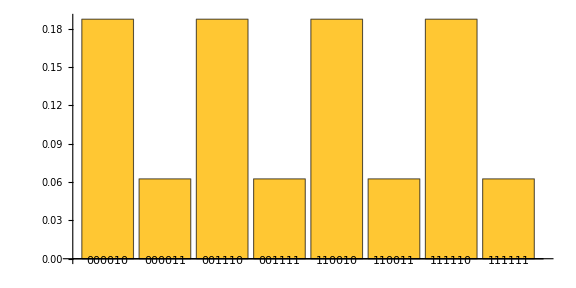

```mathematica
explorecircuit[]["ProbabilityPlot",AspectRatio->1/2]
```

### Example #2

Consider the quantum circuit below. What are the probabilities of measuring each of the 4-bit classical outcomes? Plot the probability distribution.

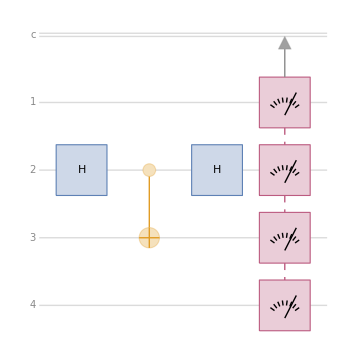

```mathematica
explorecircuit2=QuantumCircuitOperator[{"H"->2,"CNOT"->{2,3},"H"->2,"M"->Range[4]}];
explorecircuit2["Diagram"]
```

##### Solution

The non-zero probability outcomes are shown:

```mathematica
explorecircuit2[]["Probability"]
```

<|0000→1/4,0010→1/4,0100→1/4,0110→1/4|>

The entire distribution is shown:

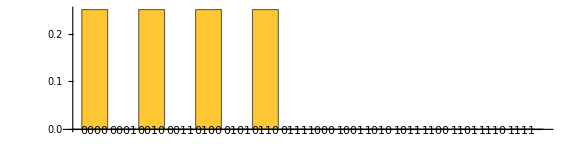

```mathematica
explorecircuit2[]["ProbabilitiesPlot",ImageSize->Large,AspectRatio->1/4]
```

### Example #3

Consider the quantum circuit below. What are the probabilities of measuring only 2nd and 4th wires? Plot the probability distribution.

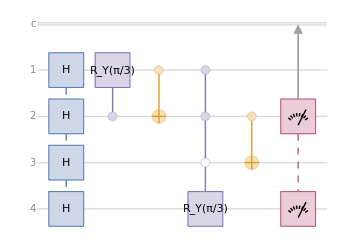

```mathematica
explorecircuit3=QuantumCircuitOperator[{"H"->Range[4],{"C","RY"[π/3]},"CNOT"->{1,2},{"C","RY"[π/3],{1,2},{3}},"CNOT"->{2,3},"M"->{2,4}}];
explorecircuit3["Diagram"]
```

##### Solution

The non-zero probability outcomes are shown:

```mathematica
explorecircuit3[]["Probability"]
```

<|00→(1/8+2 (1/8+(√3)/8)^2)/(3/8+5 (-1/8+(√3)/8)^2+5 (1/8+(√3)/8)^2),01→(1/8+2 (1/8+(√3)/8)^2)/(3/8+5 (-1/8+(√3)/8)^2+5 (1/8+(√3)/8)^2),10→(1/16+3 (-1/8+(√3)/8)^2)/(3/8+5 (-1/8+(√3)/8)^2+5 (1/8+(√3)/8)^2),11→(1/16+2 (-1/8+(√3)/8)^2+(1/8+(√3)/8)^2)/(3/8+5 (-1/8+(√3)/8)^2+5 (1/8+(√3)/8)^2)|>

The entire distribution is shown:

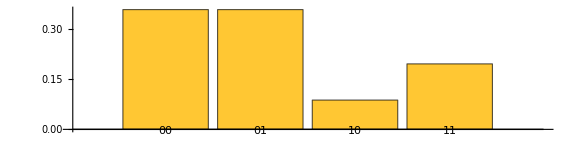

```mathematica
explorecircuit3[]["ProbabilitiesPlot",ImageSize->Large,AspectRatio->1/4]
```

## Initialization

Install Wolfram quantum framework and also the definition of binAdd function:

```mathematica
PacletInstall["https://www.wolfr.am/DevWQCF",ForceVersionInstall->True]
<<Wolfram`QuantumFramework`
```

PacletObject[…]

```mathematica
binAdd[str1_String,str2_String]/;AllTrue[{str1,str2},StringFreeQ[Except["0"|"1"]..]]:=IntegerString[FromDigits[str1,2]+FromDigits[str2,2],2]
```